# PrincipalAxisClustering

Quickly cluster a point cloud by recursive separation

## Definition

```mathematica
PrincipalAxisClustering // ClearAll;
```

### Initialization

```mathematica
$inDef = False;
$debug = True;
```

#### beginDefinition

```mathematica
beginDefinition // ClearAll;
```

```mathematica
beginDefinition // Attributes = { HoldFirst };
```

```mathematica
beginDefinition::unfinished = "\
Starting definition for `1` without ending the current one.";
```

:!CodeAnalysis::BeginBlock::

:!CodeAnalysis::Disable::SuspiciousSessionSymbol::

```mathematica
beginDefinition[ s_Symbol ] /; $debug && $inDef :=
    WithCleanup[
        $inDef = False
        ,
        Print @ TemplateApply[ beginDefinition::unfinished, HoldForm @ s ];
        beginDefinition @ s
        ,
        $inDef = True
    ];
```

:!CodeAnalysis::EndBlock::

```mathematica
beginDefinition[ s_Symbol ] :=
    WithCleanup[ Unprotect @ s; ClearAll @ s, $inDef = True ];
```

#### endDefinition

```mathematica
endDefinition // beginDefinition;
```

```mathematica
endDefinition // Attributes = { HoldFirst };
```

```mathematica
endDefinition[ s_Symbol ] := endDefinition[ s, DownValues ];
```

```mathematica
endDefinition[ s_Symbol, None ] := $inDef = False;
```

```mathematica
endDefinition[ s_Symbol, DownValues ] :=
    WithCleanup[
        AppendTo[ DownValues @ s,
                  e: HoldPattern @ s[ ___ ] :>
                      throwInternalFailure @ HoldForm @ e
        ],
        $inDef = False
    ];
```

```mathematica
endDefinition[ s_Symbol, SubValues  ] :=
    WithCleanup[
        AppendTo[ SubValues @ s,
                  e: HoldPattern @ s[ ___ ][ ___ ] :>
                      throwInternalFailure @ HoldForm @ e
        ],
        $inDef = False
    ];
```

```mathematica
endDefinition[ s_Symbol, list_List ] :=
    endDefinition[ s, # ] & /@ list;
```

```mathematica
endDefinition // endDefinition;
```

### Messages

```mathematica
PrincipalAxisClustering::internal =
"An unexpected error occurred. `1`";
```

```mathematica
PrincipalAxisClustering::matrix =
"The argument `1` is not a rectangular matrix of numeric values.";
```

```mathematica
PrincipalAxisClustering::invnarr =
"The array `1` is not valid.";
```

```mathematica
PrincipalAxisClustering::invspd =
"`1` is not a valid SpatialPointData object.";
```

```mathematica
PrincipalAxisClustering::invspdp =
"`1` does not contain valid point data.";
```

```mathematica
PrincipalAxisClustering::invcount =
"Non-negative integer or Automatic expected for the cluster count instead of
`1`.";
```

### Attributes

```mathematica
PrincipalAxisClustering // Attributes = { };
```

### Options

```mathematica
PrincipalAxisClustering // Options = { Method -> Median };
```

TODO: Possible options to implement (from FindClusters): CriterionFunction DistanceFunction FeatureExtractor FeatureNames FeatureTypes MissingValueSynthesis PerformanceGoal RandomSeeding Weights

### Main definition

```mathematica
PrincipalAxisClustering[ points_, opts: OptionsPattern[ ] ] :=
    catchTop @ PrincipalAxisClustering[ points, Automatic, opts ];
```

```mathematica
PrincipalAxisClustering[ points_, maxItems_, opts: OptionsPattern[ ] ] :=
    catchTop @ principalAxisClustering[
        checkPoints @ points,
        checkMaxItems @ maxItems,
        OptionValue @ Method
    ];
```

#### principalAxisClustering

```mathematica
principalAxisClustering // beginDefinition;
```

```mathematica
e: principalAxisClustering[ arr_NumericArray, maxItems_, method_ ] :=
    Module[ { points, clusters, type, result },
        points = Developer`ToPackedArray @ Normal @ arr;
        If[ Dimensions @ points =!= 2, throwFailure[ "matrix", arr ] ];
        If[ ! pointsQ @ points, throwFailure[ "invnarr", arr ] ];
        clusters = principalAxisClustering[ points, maxItems, method ];
        If[ ! TrueQ @ clustersQ @ clusters, throwInternalFailure @ e ];
        type = NumericArrayType @ arr;
        result = NumericArray[ #, type ] & /@ clusters
    ];
```

```mathematica
principalAxisClustering[ points_? pointsQ, maxItems_, method_ ] :=
    Block[ { axisSign = getAxisSignFunc @ method },
        paClusters[ points, maxItems ]
    ];
```

```mathematica
principalAxisClustering // endDefinition;
```

### Error cases

Invalid argument count:

```mathematica
PrincipalAxisClustering[ ] :=
    catchTop @ throwFailure[ "argm", PrincipalAxisClustering, 0, 2 ];

PrincipalAxisClustering[ a_, b_, c: Except[ OptionsPattern[ ] ], d___ ] :=
    catchTop @ throwFailure[
        "nonopt",
        c,
        2,
        HoldForm @ PrincipalAxisClustering[ a, b, c, d ]
    ];
```

Missed something that needs to be fixed:

```mathematica
e: PrincipalAxisClustering[ ___ ] :=
    catchTop @ throwInternalFailure @ e;
```

### Dependencies

#### Argument Validation

##### checkPoints

```mathematica
checkPoints // beginDefinition;
```

```mathematica
checkPoints[ points_? pointsQ ] :=
    points;
```

```mathematica
checkPoints[ arr_NumericArray ] :=
    If[ NumericArrayQ @ arr, arr, throwFailure[ "invnarr", arr ] ];
```

```mathematica
checkPoints[ spd_SpatialPointData ] := (
    If[ ! System`Private`ValidQ @ spd, throwFailure[ "invspd", spd ] ];
    If[ ! pointsQ @ spd[ "Points" ], throwFailure[ "invspdp", spd ] ];
    spd
);
```

TODO: QuantityArray StructuredArray SymmetrizedArray RawArray SparseArray Association? GeoPositions?

```mathematica
checkPoints[ other_ ] := throwFailure[ "matrix", other ];
```

```mathematica
checkPoints // endDefinition;
```

##### pointsQ

```mathematica
pointsQ // beginDefinition;
pointsQ[ points_ ] := ArrayQ[ points, 2, NumericQ ];
pointsQ[ ___     ] := False;
pointsQ // endDefinition;
```

##### clustersQ

```mathematica
clustersQ // beginDefinition;
clustersQ[ clusters_List ] := AllTrue[ clusters, pointsQ ];
clustersQ[ ___           ] := False;
clustersQ // endDefinition;
```

##### checkMaxItems

```mathematica
checkMaxItems // beginDefinition;
checkMaxItems[ n_Integer? Positive ] := n;
checkMaxItems[ UpTo[ n_Integer? Positive ] ] := n;
checkMaxItems[ Automatic ] := Automatic;
checkMaxItems[ other_ ] := throwFailure[ "invcount", other ];
checkMaxItems // endDefinition;
```

#### Clustering

##### paClusters

```mathematica
paClusters // beginDefinition;
```

```mathematica
paClusters[ points_, Automatic ] :=
    paClusters[ points, 2 ^ Floor[ Log2 @ Length @ points / 2 ] ];
```

```mathematica
paClusters[ points_, maxItems_ ] :=
    Module[ { iterations, splitter, clusters, remaining },

        iterations = Floor @ Log2 @ maxItems;
        splitter   = Flatten[ split /@ #, 1 ] &;
        clusters   = Nest[ splitter, { points }, iterations ];
        remaining  = maxItems - Length @ clusters;

        partialSplit[ clusters, remaining ]
    ];
```

```mathematica
paClusters // endDefinition;
```

##### split

```mathematica
split // beginDefinition;
```

```mathematica
split[ points_ /; Length @ points < 2 ] := { points };
```

```mathematica
split[ points_ ] :=
    Module[ { axis, sign, left, right },

        axis  = principalAxis @ points;
        sign  = axisSign[ points, axis ];
        left  = Pick[ points, sign, -1 ];
        right = Pick[ points, sign,  1 ];

        { left, right }
    ];
```

```mathematica
split // endDefinition;
```

##### partialSplit

```mathematica
partialSplit // beginDefinition;
```

```mathematica
partialSplit[ clusters_, rem_ ] /; Less[ 0, rem, Length @ clusters ] :=
    Module[ { pos, splitter },

        pos = Keys @ TakeLargestBy[
                  Association @ MapIndexed[ #2 -> #1 &, clusters ],
                  Length,
                  rem
              ];

        splitter = Composition[ Apply @ Sequence, split ];

        MapAt[ splitter, clusters, pos ]
    ];
```

```mathematica
partialSplit[ clusters_, _ ] := clusters;
```

```mathematica
partialSplit // endDefinition;
```

#### Principal Axis

##### principalAxis

```mathematica
principalAxis // beginDefinition;
```

```mathematica
principalAxis[ points_ ] :=
    First[ Eigenvectors[ Covariance @ points, UpTo[ 1 ] ],
           throwInternalFailure @ principalAxis @ points
    ];
```

```mathematica
principalAxis // endDefinition;
```

##### getAxisSignFunc

```mathematica
getAxisSignFunc // beginDefinition;
getAxisSignFunc[ Mean      ] := axisMeanSign;
getAxisSignFunc[ Median    ] := axisMedianSign;
getAxisSignFunc[ Automatic ] := axisMedianSign;
getAxisSignFunc[ other_    ] := throwFailure[ "invmethod", other ];
getAxisSignFunc // endDefinition;
```

##### axisSign

```mathematica
axisSign // ClearAll;
axisSign := getAxisSignFunc @ OptionValue[ PrincipalAxisClustering, Method ];
```

##### axisMedianSign

```mathematica
axisMedianSign // ClearAll;
```

```mathematica
axisMedianSign := axisMedianSign =
    Compile[ { { points, _Real, 2 }, { axis0, _Real, 1 } },
        Block[ { mean, shifted, axis, dotted, len, sign },

            mean    = Mean @ points;
            shifted = # - mean & /@ points;
            axis    = If[ Negative @ Total @ axis0, -axis0, axis0 ];
            dotted  = Dot[ shifted, axis ];
            len     = Length @ points;
            sign    = Sign[ dotted - Median @ dotted ];

            2 * Sign[ sign + 1 ] - 1
        ],
        RuntimeOptions    -> "Speed",
        RuntimeAttributes -> { Listable },
        Parallelization   -> True,
        CompilationTarget -> $compilationTarget
    ];
```

##### axisMeanSign

```mathematica
axisMeanSign // ClearAll;
```

```mathematica
axisMeanSign := axisMeanSign =
    Compile[ { { points, _Real, 2 }, { axis0, _Real, 1 } },
        Block[ { median, shifted, axis, dotted },

            median  = Mean @ points;
            shifted = # - median & /@ points;
            axis    = If[ Negative @ Total @ axis0, -axis0, axis0 ];
            dotted  = Dot[ shifted, axis ];

            Sign @ dotted
        ],
        RuntimeOptions    -> "Speed",
        RuntimeAttributes -> { Listable },
        Parallelization   -> True,
        CompilationTarget -> $compilationTarget
    ];
```

#### Compilation

##### $compilationTarget

```mathematica
$compilationTarget // ClearAll;
$compilationTarget := $compilationTarget = If[ noCCompilerQ[ ], "WVM", "C" ];
```

##### noCCompilerQ

```mathematica
noCCompilerQ // beginDefinition;
```

```mathematica
noCCompilerQ[ ] :=
    TrueQ @ Quiet @ Check[
        Compile[ { }, 1 + 1, CompilationTarget -> "C" ],
        True,
        {
            CCompilerDriver`CreateLibrary::nocomp,
            CCompilerDriver`CreateLibrary::instl,
            Compile::nogen
        }
    ];
```

```mathematica
noCCompilerQ // endDefinition;
```

#### Error handling

##### catchTop

```mathematica
catchTop // beginDefinition;
```

```mathematica
catchTop // Attributes = { HoldFirst };
```

```mathematica
catchTop[ eval_ ] :=
    Block[ { $catching = True, $failed = False, catchTop = # & },
        Catch[ eval, $top ]
    ];
```

```mathematica
catchTop // endDefinition;
```

##### throwFailure

```mathematica
throwFailure // beginDefinition;
```

```mathematica
throwFailure // Attributes = { HoldFirst };
```

```mathematica
throwFailure[ tag_String, params___ ] :=
    throwFailure[ MessageName[ PrincipalAxisClustering, tag ], params ];
```

```mathematica
throwFailure[ msg_, args___ ] :=
    Module[ { failure },
        failure = messageFailure[ msg, Sequence @@ HoldForm /@ { args } ];
        If[ TrueQ @ $catching,
            Throw[ failure, $top ],
            failure
        ]
    ];
```

```mathematica
throwFailure // endDefinition;
```

##### messageFailure

```mathematica
messageFailure // beginDefinition;
```

```mathematica
messageFailure // Attributes = { HoldFirst };
```

```mathematica
messageFailure[ args___ ] :=
    Module[ { quiet },
        quiet = If[ TrueQ @ $failed, Quiet, Identity ];
        WithCleanup[
            quiet @ ResourceFunction[ "MessageFailure" ][ args ],
            $failed = True
        ]
    ];
```

```mathematica
messageFailure // endDefinition;
```

##### throwInternalFailure

```mathematica
throwInternalFailure // beginDefinition;
```

```mathematica
throwInternalFailure // Attributes = { HoldFirst };
```

```mathematica
throwInternalFailure[ eval_, a___ ] :=
    throwFailure[
        PrincipalAxisClustering::internal,
        $bugReportLink,
        HoldForm @ eval,
        a
    ];
```

```mathematica
throwInternalFailure // endDefinition;
```

##### $bugReportLink

```mathematica
$bugReportLink := $bugReportLink = Hyperlink[
    "Report this issue »",
    URLBuild @ <|
        "Scheme"   -> "https",
        "Domain"   -> "resources.wolframcloud.com",
        "Path"     -> { "FunctionRepository", "feedback-form" },
        "Fragment" -> SymbolName @ PrincipalAxisClustering
    |>
];
```

## Documentation

### Usage

PrincipalAxisClustering[{{p_11,p_12,…},{p_21,p_22,…},…}]

recursively partitions the given points into approximately equal-sized clusters along their principal axis.

PrincipalAxisClustering[points,n]

partitions points into at most n clusters.

### Details & Options

PrincipalAxisClustering[points] is equivalent to PrincipalAxisClustering[points,Automatic].

If n is a power of two, the clusters will be approximately equal-sized.

PrincipalAxisClustering accepts a Method option which decides how to separate points according to their projected values on the principal axis.

The value for Method can be one of the following:

Median | separate points into approximately equal-sized clusters
Mean | separate points at the center of mass

## Examples

```mathematica
Get @ FileNameJoin @ { NotebookDirectory[ ], "Definition.wl" };
TestReport @ FileNameJoin @ { NotebookDirectory[ ], "Tests.wlt" }
```

TestReportObject[…]

### Basic Examples

Cluster one-dimensional data:

```mathematica
PrincipalAxisClustering[{{1},{2},{10},{12},{3},{1},{13},{25}}]
```

{{{1},{2},{3},{1}},{{10},{12},{13},{25}}}

Find exactly four clusters:

```mathematica
PrincipalAxisClustering[{{1},{2},{10},{12},{3},{1},{13},{25}},4]
```

{{{1},{1}},{{2},{3}},{{10},{12}},{{13},{25}}}

Cluster vectors of real values:

```mathematica
PrincipalAxisClustering[{{2.5,3.1},{5.9,3.4},{10,15},{2.2,1.5},{100,7.5}}]
```

{{{2.5,3.1},{2.2,1.5}},{{5.9,3.4},{10,15},{100,7.5}}}

### Scope

Partition a 3D point cloud:

```mathematica
mesh=ResourceData["Stanford Bunny","MeshRegion"]
```

-Graphics-

```mathematica
ListPointPlot3D[PrincipalAxisClustering[RandomPoint[mesh,10000]],]
```

-Graphics-

Cluster high dimensional data:

```mathematica
points=RandomReal[1,{10000,100}];
First[AbsoluteTiming[PrincipalAxisClustering[points]]]
```

0.141511

### Options

#### Method

With the default setting of Method→Median, clusters are likely to span across gaps:

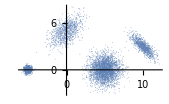

```mathematica
ListPlot[data=]
```

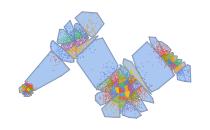

```mathematica
c1=PrincipalAxisClustering[data,Method->Median];
Show[RegionUnion@@ConvexHullMesh/@c1,ListPlot[c1]]
```

Using Method→Mean can improve separation:

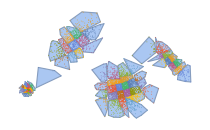

```mathematica
c2=PrincipalAxisClustering[data,Method->Mean];
Show[RegionUnion@@ConvexHullMesh/@c2,ListPlot[c2]]
```

However, Mean will tend to produce unbalanced cluster sizes compared to Median:

```mathematica
Length/@c1
```

{93,94,94,94,93,94,94,94,93,94,94,94,93,94,94,94,93,94,94,94,93,94,94,94,93,94,94,94,93,94,94,94,93,94,94,94,93,94,94,94,93,94,94,94,93,94,94,94,93,94,94,94,93,94,94,94,93,94,94,94,93,94,94,94}

```mathematica
Length/@c2
```

{42,57,66,86,57,54,76,58,77,95,89,65,69,65,43,5,35,44,48,29,34,46,57,32,75,98,126,112,114,131,91,80,131,161,180,203,132,137,223,167,159,199,182,111,200,189,170,130,39,45,43,39,28,47,23,46,73,102,121,129,132,121,102,80}

### Applications

Downsample a large point cloud by choosing nicely spaced representative points:

```mathematica
points=RandomPoint[ResourceData["Stanford Bunny","MeshRegion"],100000];
```

```mathematica
Graphics3D[Point[Median/@PrincipalAxisClustering[points,1000]]]
```

-Graphics-

Compare to random sampling:

```mathematica
Graphics3D[Point[RandomSample[points,1000]]]
```

-Graphics-

### Properties and Relations

The axis representing each cluster separation corresponds to the first component in PrincipalComponents:

```mathematica
points=N[Position[ImageData[-Graphics-],1,{2}]];
```

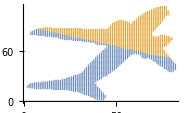

```mathematica
ListPlot[PrincipalAxisClustering[points,2]]
```

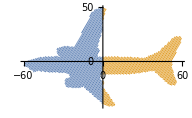

```mathematica
ListPlot[SplitBy[SortBy[PrincipalComponents[points],First],Negative@*First]]
```

The principal axis can be obtained from the Eigenvectors of the Covariance matrix:

```mathematica
pa=First[Eigenvectors[Covariance[points],UpTo[1]]]
```

{0.439069,0.898453}

Visualize the axis over the original data:

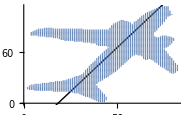

```mathematica
ListPlot[points,Epilog->Style[InfiniteLine[Mean[points],pa],Red]]
```

Projecting the standardized points onto the principal axis gives scalar values that indicate which cluster they belong to:

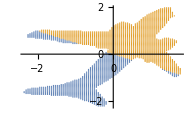

```mathematica
ListPlot[GatherBy[Standardize[points],Negative[#.pa]&]]
```

PrincipalAxisClustering finds clusters very quickly:

```mathematica
points=;
Dimensions[points]
```

{11169,2}

This is pretty much the whole point of the function:

```mathematica
First@RepeatedTiming[c1=PrincipalAxisClustering[points,16]]
```

0.00725512

Compare to FindClusters:

```mathematica
First@RepeatedTiming[c2=FindClusters[points,16]]
```

3.18662

PrincipalAxisClustering gives clusters that better represent the local point cloud density:

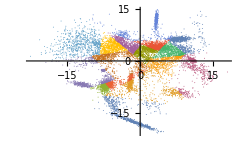

```mathematica
ListPlot[c1]
```

FindClusters represents better separation of the data:

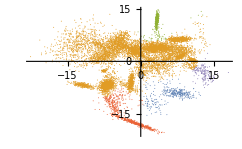

```mathematica
ListPlot[c2]
```

PrincipalAxisClustering partitions points into non-overlapping convex regions:

```mathematica
clusters=PrincipalAxisClustering[RandomVariate[BinormalDistribution[0],20000]];
```

```mathematica
Show[RegionUnion@@ConvexHullMesh/@clusters,ListPlot[clusters],PlotRange->2]
```

-Graphics-

The number of clusters locally scales with the point cloud density:

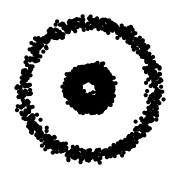

```mathematica
Graphics[Point[points=]]
```

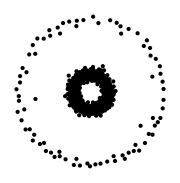

```mathematica
Graphics[Point[Median/@PrincipalAxisClustering[points,500]]]
```

### Possible Issues

If the number of requested clusters is not a power of two, then cluster sizes will not be well balanced:

```mathematica
points=RandomReal[1,{100,2}];
```

```mathematica
Length/@PrincipalAxisClustering[points,5]
```

{12,13,25,25,25}

```mathematica
Length/@PrincipalAxisClustering[points,8]
```

{12,13,12,13,12,13,12,13}

### Neat Examples

Visualize the recursive nature of the clustering:

```mathematica
data=RandomReal[{-1,1},{10^4,2}];
```

```mathematica
plots=Table[ListPlot[PrincipalAxisClustering[data,2^n],],{n,0,5}];
```

```mathematica
GraphicsGrid[Partition[plots,3]]
```

-Graphics-

Partition a point cloud into clusters:

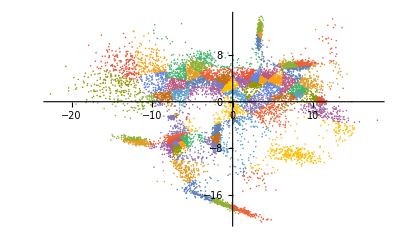

```mathematica
points=;
ListPlot[clusters=PrincipalAxisClustering[points]]
```

Remove some outliers from each cluster:

```mathematica
filterOutliers[cluster_,q_]:=
Module[{m,d,t},
m=Mean[cluster];
d=Norm[#-m]&/@cluster;
t=Quantile[d,1-q];
Pick[cluster,#<t&/@d]
];
```

```mathematica
filtered=filterOutliers[#,.3]&/@clusters;
```

```mathematica
expand[cluster_,s_]:=
With[{m=Mean[cluster]},
m+s(#-m)&/@cluster
];
```

Construct a parameterized topological representation of the point cloud:

```mathematica
Manipulate[Show[RegionUnion@@(ConvexHullMesh[expand[#,e]]&/@filtered),ListPlot[points]],{{e,1},0.01,5}]
```

-Graphics-

## Source & Additional Information

### Contributed By

Richard Hennigan (Wolfram Research)

### Keywords

point cloud

downsample

simplify data

sampling

density clustering

eigenvector

### Categories

3D Visualization |  Accessibility
 Array Manipulation |  Cloud & Deployment
 Core Language & Structure |  Data Manipulation & Analysis
 Engineering Data & Computation |  External Interfaces & Connections
 Financial Data & Computation |  Geographic Data & Computation
 Geometry |  Graphs & Networks
 Higher Mathematical Computation |  Images
 Just For Fun |  Knowledge Representation & Natural Language
 Machine Learning |  Notebook Documents & Presentation
 Programming Utilities |  Repository Tools
 Scientific and Medical Data & Computation |  Social, Cultural & Linguistic Data
 Sound & Video |  Strings & Text
 Symbolic & Numeric Computation |  System Operation & Setup
 Time-Related Computation |  User Interface Construction
 Visualization & Graphics |  Wolfram Physics Project

### Related Symbols

FindClusters

Covariance

Eigenvectors

### Related Resource Objects

QuadtreeImageDecomposition

Equisample

MultidimensionalScaling

NonConvexHullMesh

LloydAlgorithm

### Source/Reference Citation

Source, reference or citation information

### Links

PrincipalAxisClustering | rhennigan/ResourceFunctions | GitHub

Guide: Cluster Analysis

Guide: Machine Learning

### Tests

#### Initialization

```mathematica
VerificationTest[
    SetOptions[ ResourceFunction[ "MessageFailure" ], "TestMode" -> True ],
    KeyValuePattern[ "TestMode" -> True ],
    SameTest -> MatchQ
]
```

#### Tests

```mathematica
VerificationTest[
    points = RandomReal[ 1, { 128, 2 } ];,
    Null
]
```

```mathematica
VerificationTest[
    Length[ clusters = PrincipalAxisClustering[ points, 10 ] ],
    10
]
```

```mathematica
VerificationTest[
    Sort @ points === Sort @ Flatten[ clusters, 1 ],
    True
]
```

```mathematica
VerificationTest[
    Sort[
        Length /@ PrincipalAxisClustering[ RandomReal[ 1, { 128, 2 } ], 10 ]
    ],
    { 8, 8, 8, 8, 16, 16, 16, 16, 16, 16 }
]
```

```mathematica
VerificationTest[
    Apply[
        SameQ,
        Map[
            Length,
            PrincipalAxisClustering[
                RandomReal[ 1, { 2^RandomInteger[10], 2 } ],
                Method -> Median
            ]
        ]
    ],
    True
]
```

##### Error Cases

#### Cleanup

```mathematica
VerificationTest[
    SetOptions[ ResourceFunction[ "MessageFailure" ], "TestMode" -> False ],
    KeyValuePattern[ "TestMode" -> False ],
    SameTest -> MatchQ
]
```

### Compatibility

#### Wolfram Language Version

12.3+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session |  ScriptScript run in batch mode |  SubkernelParallel or grid subkernel
 WebEvaluationCloud evaluation initiated by an HTTP request |  WebAPIAPI called through an HTTP request |  ScheduledScheduled task
 BatchJobRemote batch job |  |

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

This is mostly meant to support another function that I'll be submitting, but it seemed useful enough on its own to submit separately.